```mathematica
CalcWindow=10;
N0=2047;
h=0.00000001;
N0=N0+Boole[EvenQ[N0]];
Box2Imp[T0_]:=Table[N[UnitBox[t/T0]],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
BoxAmp2Imp[Energy_,T0_]:=Box2Imp[T0]×√(Energy/NIntegrate[Interpolation[Transpose[{Table[t,{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}],Box2Imp[T0, CalcWindow, N0]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}]);
β2=25.;γ=5.8;α=-1900.;L=0.003;
```

```mathematica
Imp0=BoxAmp2Imp[12,1];
Imp=Fourier[Imp0];
```

```mathematica
D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp=Exp[I β2/2 D2Fourier h];
SpatialOp[x_List]=Exp[I γ Abs[x]^2 h];
GainOp=Exp[-α/2 h];
ListPlot[(Abs[InverseFourier[Imp]]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow, CalcWindow},AxesOrigin->{-CalcWindow,0}];
```

```mathematica
Imp=Sqrt[FourierOp]Imp;
Imp=Imp Sqrt[GainOp];
Monitor[
For[ξ=h/2,ξ<L,ξ+=h,
Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];
Imp=FourierOp Imp;
Imp=Imp GainOp;

],Round[100 ξ/L]]
Imp=InverseFourier[Imp/Sqrt[FourierOp]];
Imp=Imp Sqrt[GainOp];
```

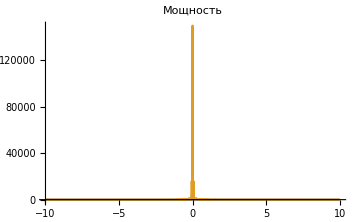
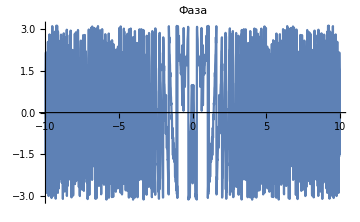
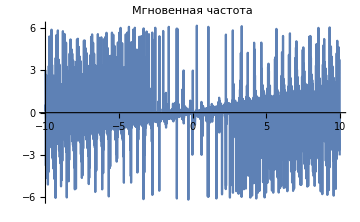

```mathematica
{ListPlot[{(Abs[Imp0]^2),(Abs[Imp]^2)},PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Мощность",ImageSize->Medium],
ListPlot[(Arg[Imp]),PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Фаза",ImageSize->Medium],
ListPlot[(Differences[Arg[Imp]]),PlotRange->Automatic,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Мгновенная частота",ImageSize->Medium]}
```